# Highly-cited articles

## 登録論文数累積

edgestat-refcount-cumulative.nb より。

```mathematica
artcountAcm={331362,866254,1415896,2141764,3156527,4323230,5675522,7217673,9135438,11279956,13673661,16645203,20421796,25376280,31440632}
```

{331362,866254,1415896,2141764,3156527,4323230,5675522,7217673,9135438,11279956,13673661,16645203,20421796,25376280,31440632}

## 累積世代ごとの主要論文

```mathematica
mainartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt1Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt1Perc.save}

```mathematica
Map[Get,mainartfiles];
```

### 主要論文

主要論文と被引用数

```mathematica
top1PcCitedArtList=Table[Reverse[SortBy[Flatten[Map[#[[2]]&,topCitingCitedArt1Perc[n,"citing rule"],{2}]]//Tally,#[[2]]&]],{n,1950,2020,5}];
```

主要論文数

```mathematica
top1PcCitedArtCount=Map[Length,top1PcCitedArtList]
```

{10,30,46,50,38,33,32,26,19,22,33,66,192,315,336}

全論文数における主要論文数割合（%）

```mathematica
top1pcArtRatio=top1PcCitedArtCount/artcountAcm*100//N
```

{0.00301785,0.00346319,0.00324883,0.00233452,0.00120385,0.000763318,0.000563825,0.000360227,0.000207981,0.000195036,0.00024134,0.000396511,0.000940172,0.00124132,0.00106868}

### 新規出現論文

```mathematica
FoldList[Composition[Union,Flatten,List],{},Map[#[[1]]&,top1PcCitedArtList,{2}]];
```

新規出現主要論文ID

```mathematica
newcomerCitedArt=Map[Complement[#[[2]],#[[1]]]&,Partition[FoldList[Composition[Union,Flatten,List],{},Map[#[[1]]&,top1PcCitedArtList,{2}]],2,1]]
```

{{16694480,16694558,16695228,16747456,16747508,16747784,17247100,17247150,17751251,18016252},{14772207,14822727,14907713,15395398,15398090,15398551,16561366,16695286,16695568,16745305,16746620,16747230,16747652,16747674,16747907,16747948,16748220,16748273,16748381,16991878,17760012,18128147},{12989928,12991232,12991237,12996882,13069686,13124776,13130792,13186838,13319380,14381428,14803635,14862161,14873923,14898516,14907661,14915960,14927794,15392854,15395569,15404816,15410483,15421999,15436457,16991506,16994401},{13249955,13262900,13276348,13286333,13293190,13428781,13475399,13563554,13610936,13718526,13764136,13975866,13986422,14381429,14454024,14775715,14794694,14848424,14927572,14938350},{13610928,13641241,13675766,13767412,13772379,13944428,14240539,14287192,14474176},{13267987,13278318,13672998,13910995,16654194,4956917,5806584},{1195397,13671378,14097352,4850204,4887011,5432063,5962951,773363},{236308,265521,271968,388356,388439,4326772,6159641,6246368,881736,942051},{518835,6312838},{2440339,2448875,2985470,6270629,6546423},{2231712,4705382,6336730,6828386,6960240,7108955},{1172191,149110,2025413,2199796,2659436,3162770,322279,3323813,344137,3447015,3838314,3843705,3881765,4179068,4291934,4504350,6091052,6166661,6235151,6266278,6295879,6310323,6326095,6329026,6345791,7984417,9254694},{10069079,10547847,10592235,10647931,10655437,10802651,10829079,1105573,11130711,11181995,11237011,11309499,11328886,11368702,11373684,11498575,11524383,1175627,11846609,1202204,12466850,12748199,12824337,12912839,12925520,13650640,13688369,1400587,14399272,14450081,14530136,14744438,15034147,15260895,15297300,15299374,15299926,15461798,1555235,15572765,15761078,1593914,16255080,16595758,17237035,17488738,17554300,18156677,18287387,1852778,19171970,2439888,2449095,2744487,27754618,28561359,2868172,291033,2999980,3047011,320200,3327686,3344216,3358796,3537305,3558716,3670292,3692487,3714490,3806354,3899825,4202581,4337382,4366476,4598299,4896022,5146491,5700707,5963888,603028,6198242,6232463,6253831,6260957,6269464,6286831,6295880,6310324,6329717,6606682,6610841,6667333,6791577,6880820,7138600,7219534,7463489,7494007,8223268,8242752,8254673,8366922,843571,8520220,8744570,8744573,8902363,9177342,922889,9278503,9367129,9396791,9486653,9504803,9521319,9521921,9634230,9717241,9742976,9757107,9843981,9887164,9918953},{10075613,10102814,10109801,10592173,10638745,10797032,10827456,10835412,10963602,11152613,11209064,11234459,11283309,11553815,11556941,11689955,11752295,11771995,11823860,11832527,11904577,11932250,11994752,12045153,12068308,12111919,12117397,12130773,12184808,12297042,1244564,12485966,12490959,12538238,12629218,12734009,12883005,12958120,13298683,13655060,13726518,14597658,14656957,15111519,15118073,15118125,15173120,15175435,15223320,15264254,15372042,15501092,15652477,15758009,15939837,15944708,16056220,16081474,16199517,16222654,16497588,16646809,16862161,16904174,16928733,17320507,17483113,17512414,1759558,17618441,17634462,17681537,17701901,17846036,17996036,18029452,18035408,18261238,18349386,18485877,18516045,18546601,18772890,18839484,19015660,19033363,19097774,19131956,19167326,19261174,19289445,19325852,1932883,19451168,19461840,19474385,19505943,19565683,19801464,19812666,20057044,20124692,20124702,20354512,20383002,20383131,20436464,20525992,20610543,20644199,20979621,20981092,21296855,21351269,21376230,21460441,21546353,2188735,22237781,22930834,22955616,23335087,24132122,24399786,24889800,2513255,2748771,3397865,3616518,36810,3798106,3802833,3928249,4561027,6668417,7063747,7786990,7814313,7984236,8252621,8421494,8524021,8589427,8628042,8721797,8779443,8812068,9023104,9176952,9305837,9310563,9521922,9623998,9759494,9804556,9881538,9916792,9944570},{10062328,10789670,11253156,12377157,12391568,12900694,15102499,15273542,15817019,15969739,16055882,16204405,16820507,16923388,16923606,17183312,17486113,17586664,17695343,17872937,1798888,18650514,18650914,18798982,18929686,19029910,19114008,19246619,19346325,19414839,19460998,19487818,19499576,19621072,19622511,19622551,19805654,19910308,19945376,20003500,20080505,20110278,20513432,20525638,20601685,20709691,21221095,21478889,21572440,21700674,21816040,21959131,21988835,22008217,22357727,22383036,22388286,22437870,22506599,22543367,22588877,22658127,22743772,22745249,22820204,23000897,23104886,23128226,23193283,23245604,23287718,23329690,23550210,23618408,24141714,24451623,24695404,25220842,25260700,25516281,25554246,25559415,25567568,25605792,25651787,25741868,26432245,26742998,26808342,26903338,27004904,27535533,28055103,29313949,30207593,30620402,31978945,31986264,32007143,3203132,32031570,32109013,32171076,9931268}}

新規出現主要論文数

```mathematica
newcomerCitedArtCount=Map[Length,newcomerCitedArt]
```

{10,22,25,20,9,7,8,10,2,5,6,27,123,158,104}

主要論文数における新規出現論文数割合（%）

```mathematica
newcomerratio=newcomerCitedArtCount/top1PcCitedArtCount*100//N
```

{100.,73.3333,54.3478,40.,23.6842,21.2121,25.,38.4615,10.5263,22.7273,18.1818,40.9091,64.0625,50.1587,30.9524}

### plot

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
ListPlot[{top1PcCitedArtCount,newcomerCitedArtCount},Joined->True,PlotRange->Full,Frame->True,FrameTicks->{Automatic,{genticks,None}},PlotLabels->{"主要論文数","新規出現主要論文数"}]
```

-Graphics-

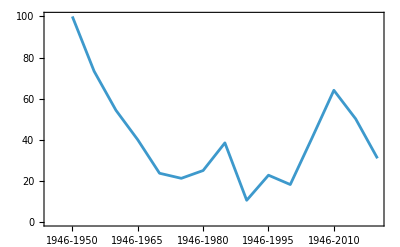
-Graphics-新規出現主要論文の全主要論文に占める割合（%）

```mathematica
Labeled[ListPlot[newcomerratio,Joined->True,Frame->True,FrameTicks->{Automatic,{genticks,None}}],"新規出現主要論文の全主要論文に占める割合（%）"]
```

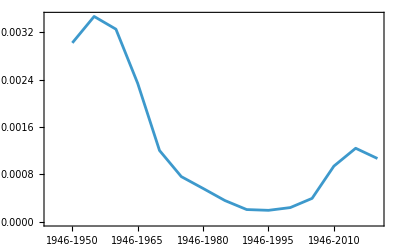
-Graphics-主要論文の全論文に占める割合（%）

```mathematica
Labeled[ListPlot[top1pcArtRatio,Joined->True,Frame->True,FrameTicks->{Automatic,{genticks,None}}],"主要論文の全論文に占める割合（%）"]
```

## 主要論文タイトル

プログラム

```mathematica
st=Import["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/pubmed24n0080.xml.blk","String"];
```

```mathematica
st1=Drop[StringSplit[st,"<PubmedArticle>"],1];
```

```mathematica
st2=Map[StringSplit[#,"\n"]&,StringSplit[st1,"\n--\n"],{2}];
```

```mathematica
st3=Map[StringReplace[#,RegularExpression["\\[\\[\\[.*\\]\\]\\]"]->""]&,st2,{3}];
```

```mathematica
titlecase[l_]:=Cases[l,{x_,y_}/;StringMatchQ[x,"<PMID *"]||StringMatchQ[x,"<ArticleTitle>"]]
```

```mathematica
(st3case=Map[titlecase,st3])//Length
```

30000

```mathematica
st3case2=Map[#[[1;;2]]&,Select[st3case,Length[#]>=2&]]
```

```mathematica
st3rule=MapApply[Rule,Map[#[[2]]&,st3case2,{2}]]
```

```mathematica
blkToTitleRule[file_String]:=Module[{st,st1,st2,st3,st3case,st3case2,st3rule},
st=Import[file,"String"];
st1=Drop[StringSplit[st,"<PubmedArticle>"],1];
st2=Map[StringSplit[#,"\n"]&,StringSplit[st1,"\n--\n"],{2}];
st3=Map[StringReplace[#,RegularExpression["\\[\\[\\[.*\\]\\]\\]"]->""]&,st2,{3}];

st3case=Map[titlecase,st3];
st3case2=Map[#[[1;;2]]&,Select[st3case,Length[#]>=2&]];
st3rule=MapApply[Rule,Map[#[[2]]&,st3case2,{2}]]
]
```

プログラム適応

```mathematica
(blks=FileNames["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/*blk"])//Length
```

1219

```mathematica
AbsoluteTiming[(pmidToTitle=Association[Flatten[ParallelMap[blkToTitleRule,blks]]]);]
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save",pmidToTitle]*)
```

高被引用論文タイトル

```mathematica
top1pctitle=Map[pmidToTitle[#[[1]]]&,top1PcCitedArtList,{2}]
```

{{Qualitative analysis of proteins: a partition chromatographic method using paper.,Mutations of Bacteria from Virus Sensitivity to Virus Resistance.,The biochemistry of bacterial toxins: The lecithinase activity of Cl. welchii toxins.,CLINICAL STUDIES OF THE BLOOD VOLUME. IV. ADAPTATION OF THE METHOD TO THE PHOTOELECTRIC MICROCOLORIMETER.,CLINICAL STUDIES OF THE BLOOD VOLUME. I. CLINICAL APPLICATION OF A METHOD EMPLOYING THE AZO DYE "EVANS BLUE" AND THE SPECTROPHOTOMETER.,A steam distillation apparatus suitable for micro-Kjeldahl analysis.,THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.,Bacteriophage-Resistant Mutants in Escherichia Coli.,Pulmonary Calcification in Negative Reactors to Tuberculin.,The Biological Actions and Therapeutic Applications of the B-Chloroethyl Amines and Sulfides.},{Qualitative analysis of proteins: a partition chromatographic method using paper.,Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.,A steam distillation apparatus suitable for micro-Kjeldahl analysis.,The free amino groups of insulin.,A colorimetric method for the determination of glucosamine and chondrosamine.,Separation of the phosphoric esters on the filter paper chromatogram.,THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.,A study of the behaviour of some sixty amino-acids and other ninhydrin-reacting substances on phenol-;collidine' filter-paper chromatograms, with notes as to the occurrence of some of them in biological fluids.,The estimation of phosphorus.,Mutations of Bacteria from Virus Sensitivity to Virus Resistance.,An improved method for the colorimetric determination of phosphate.,The pharmacological actions of polymethylene bistrimethyl-ammonium salts.,CLINICAL STUDIES OF THE BLOOD VOLUME. I. CLINICAL APPLICATION OF A METHOD EMPLOYING THE AZO DYE "EVANS BLUE" AND THE SPECTROPHOTOMETER.,[Proceedings of electrophoretic determination of blood proteins on filter paper].,Studies on cholinesterase: 3. Specific tests for true cholinesterase and pseudo-cholinesterase.,THE NITROUS OXIDE METHOD FOR THE QUANTITATIVE DETERMINATION OF CEREBRAL BLOOD FLOW IN MAN: THEORY, PROCEDURE AND NORMAL VALUES.,The total nitrogen content of egg albumin and other proteins.,The effect of sodium ions on the electrical activity of giant axon of the squid.,The identification of lower peptides in complex mixtures.,THE ESTIMATION OF HEPATIC BLOOD FLOW IN MAN.,CLINICAL STUDIES OF THE BLOOD VOLUME. IV. ADAPTATION OF THE METHOD TO THE PHOTOELECTRIC MICROCOLORIMETER.,Paper Chromatography Using Capillary Ascent.,Bacteriophage-Resistant Mutants in Escherichia Coli.,Protein measurement with the Folin phenol reagent.,The estimation of adrenaline and allied substances in blood.,Purification and properties of cytochrome c.,Simultaneous Adaptation: A New Technique for the Study of Metabolic Pathways.,Sickle cell anemia a molecular disease.,[Electrophoresis of proteins on filter paper].,The biochemistry of bacterial toxins: The lecithinase activity of Cl. welchii toxins.},{Protein measurement with the Folin phenol reagent.,A study of fixation for electron microscopy.,Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.,Qualitative analysis of proteins: a partition chromatographic method using paper.,A steam distillation apparatus suitable for micro-Kjeldahl analysis.,Separation of the phosphoric esters on the filter paper chromatogram.,The estimation of phosphorus.,An improved method for the colorimetric determination of phosphate.,A colorimetric method for the determination of glucosamine and chondrosamine.,The free amino groups of insulin.,A small particulate component of the cytoplasm.,THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.,An analysis of the end-plate potential recorded with an intracellular electrode.,Methods of paper chromatography of steroids applicable to the study of steroids in mammalian blood and tissues.,Chromatography of amino acids on sulfonated polystyrene resins.,[Proceedings of electrophoretic determination of blood proteins on filter paper].,The effect of sodium ions on the electrical activity of giant axon of the squid.,A study of the behaviour of some sixty amino-acids and other ninhydrin-reacting substances on phenol-;collidine' filter-paper chromatograms, with notes as to the occurrence of some of them in biological fluids.,A study in microtomy for electron microscopy.,Liver microsomes; an integrated morphological and biochemical study.,The total nitrogen content of egg albumin and other proteins.,Mutants of Escherichia coli requiring methionine or vitamin B12.,[Quantitative determination of blood proteins by paper electrophoresis].,Plaque formation and isolation of pure lines with poliomyelitis viruses.,Mutations of Bacteria from Virus Sensitivity to Virus Resistance.,Localization of antigen in tissue cells; improvements in a method for the detection of antigen by means of fluorescent antibody.,THE NITROUS OXIDE METHOD FOR THE QUANTITATIVE DETERMINATION OF CEREBRAL BLOOD FLOW IN MAN: THEORY, PROCEDURE AND NORMAL VALUES.,Microelectrophoresis of protein on filter-paper.,Sickle cell anemia a molecular disease.,Electrophoresis of proteins on filter paper.,Potassium accumulation in muscle and associated changes.,The estimation of adrenaline and allied substances in blood.,Chromatographic studies of nucleic acids; a technique for the identification and estimation of purine and pyrimidine bases, nucleosides and related substances.,The adsorption of proteins on erythrocytes treated with tannic acid and subsequent hemagglutination by antiprotein sera.,CLINICAL STUDIES OF THE BLOOD VOLUME. I. CLINICAL APPLICATION OF A METHOD EMPLOYING THE AZO DYE "EVANS BLUE" AND THE SPECTROPHOTOMETER.,Nerve endings in mammalian muscle.,The nucleic acids of plant tissues; the extraction and estimation of desoxypentose nucleic acid and pentose nucleic acid.,The pharmacological actions of polymethylene bistrimethyl-ammonium salts.,THE ESTIMATION OF HEPATIC BLOOD FLOW IN MAN.,The recording of potentials from motoneurones with an intracellular electrode.,The determination of hydroxyproline.,An electron microscope study of the mitochondrial structure.,A quantitative description of membrane current and its application to conduction and excitation in nerve.,The properdin system and immunity. I. Demonstration and isolation of a new serum protein, properdin, and its role in immune phenomena.,The fine structure of mitochondria.,The normal membrane potential of frog sartorius fibers.},{Protein measurement with the Folin phenol reagent.,A study of fixation for electron microscopy.,Improvements in epoxy resin embedding methods.,Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.,Separation of the phosphoric esters on the filter paper chromatogram.,A steam distillation apparatus suitable for micro-Kjeldahl analysis.,The estimation of phosphorus.,Qualitative analysis of proteins: a partition chromatographic method using paper.,A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.,An improved method for the colorimetric determination of phosphate.,Staining of tissue sections for electron microscopy with heavy metals.,Localization of antigen in tissue cells; improvements in a method for the detection of antigen by means of fluorescent antibody.,Genetic regulatory mechanisms in the synthesis of proteins.,[A micro-method of immuno-electrophoresis].,A colorimetric method for the determination of glucosamine and chondrosamine.,Zone electrophoresis in starch gels:  group variations in the serum proteins of normal human adults.,Plaque formation and isolation of pure lines with poliomyelitis viruses.,The effect of sodium ions on the electrical activity of giant axon of the squid.,Effects of varying the vehicle for OsO4 in tissue fixation.,A relation between non-esterified fatty acids in plasma and the metabolism of glucose.,The adsorption of proteins on erythrocytes treated with tannic acid and subsequent hemagglutination by antiprotein sera.,Detection of sugars on paper chromatograms.,A simple method for the isolation and purification of total lipides from animal tissues.,An analysis of the end-plate potential recorded with an intracellular electrode.,Mutants of Escherichia coli requiring methionine or vitamin B12.,Simple methods for "staining with lead" at high pH in electron microscopy.,The free amino groups of insulin.,A small particulate component of the cytoplasm.,Methods of paper chromatography of steroids applicable to the study of steroids in mammalian blood and tissues.,Liver microsomes; an integrated morphological and biochemical study.,A quantitative description of membrane current and its application to conduction and excitation in nerve.,Staining of tissue sections for electron microscopy with heavy metals. II. Application of solutions containing lead and barium.,Tissue fractionation studies.  6.  Intracellular distribution patterns of enzymes in rat-liver tissue.,THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.,The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.,Chromatography of amino acids on sulfonated polystyrene resins.,Notes on sugar determination.,A press for disrupting bacteria and other micro-organisms.,Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.,Potassium accumulation in muscle and associated changes.,Replica plating and indirect selection of bacterial mutants.,[Proceedings of electrophoretic determination of blood proteins on filter paper].,The determination of hydroxyproline.,The fine structure of neurons.,A revision of the Schoenheimer-Sperry method for cholesterol determination.,Mutations of Bacteria from Virus Sensitivity to Virus Resistance.,The nucleic acids of plant tissues; the extraction and estimation of desoxypentose nucleic acid and pentose nucleic acid.,A study of the behaviour of some sixty amino-acids and other ninhydrin-reacting substances on phenol-;collidine' filter-paper chromatograms, with notes as to the occurrence of some of them in biological fluids.,The total nitrogen content of egg albumin and other proteins.,[Quantitative determination of blood proteins by paper electrophoresis].},{Protein measurement with the Folin phenol reagent.,Improvements in epoxy resin embedding methods.,The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.,A study of fixation for electron microscopy.,A simple method for the isolation and purification of total lipides from animal tissues.,A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.,Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.,Staining of tissue sections for electron microscopy with heavy metals.,[A micro-method of immuno-electrophoresis].,Genetic regulatory mechanisms in the synthesis of proteins.,Simple methods for "staining with lead" at high pH in electron microscopy.,Detection of sugars on paper chromatograms.,Plaque formation and isolation of pure lines with poliomyelitis viruses.,Chromosome preparations of leukocytes cultured from human peripheral blood.,Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.,Zone electrophoresis in starch gels:  group variations in the serum proteins of normal human adults.,Mutants of Escherichia coli requiring methionine or vitamin B12.,Amino acid metabolism in mammalian cell cultures.,A relation between non-esterified fatty acids in plasma and the metabolism of glucose.,A quantitative description of membrane current and its application to conduction and excitation in nerve.,Separation of the phosphoric esters on the filter paper chromatogram.,The estimation of phosphorus.,Effects of varying the vehicle for OsO4 in tissue fixation.,Tissue fractionation studies.  6.  Intracellular distribution patterns of enzymes in rat-liver tissue.,Localization of antigen in tissue cells; improvements in a method for the detection of antigen by means of fluorescent antibody.,A method for determining the sedimentation behavior of enzymes: application to protein mixtures.,A steam distillation apparatus suitable for micro-Kjeldahl analysis.,Junctional complexes in various epithelia.,A SIMPLIFIED LEAD CITRATE STAIN FOR USE IN ELECTRON MICROSCOPY.,An improved method for the colorimetric determination of phosphate.,The adsorption of proteins on erythrocytes treated with tannic acid and subsequent hemagglutination by antiprotein sera.,Phosphorus assay in column chromatography.,The effect of sodium ions on the electrical activity of giant axon of the squid.,A modified procedure for lead staining of thin sections.,DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.,A colorimetric method for the determination of glucosamine and chondrosamine.,Electron microscope study of DNA-containing plasms. II. Vegetative and mature phage DNA as compared with normal bacterial nucleoids in different physiological states.,Qualitative analysis of proteins: a partition chromatographic method using paper.},{Protein measurement with the Folin phenol reagent.,The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.,Improvements in epoxy resin embedding methods.,A simple method for the isolation and purification of total lipides from animal tissues.,A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.,Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.,DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.,A study of fixation for electron microscopy.,[A micro-method of immuno-electrophoresis].,Staining of tissue sections for electron microscopy with heavy metals.,The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.,Immunochemical quantitation of antigens by single radial immunodiffusion.,A SIMPLIFIED LEAD CITRATE STAIN FOR USE IN ELECTRON MICROSCOPY.,Amino acid metabolism in mammalian cell cultures.,Mutants of Escherichia coli requiring methionine or vitamin B12.,Plaque formation and isolation of pure lines with poliomyelitis viruses.,Chromosome preparations of leukocytes cultured from human peripheral blood.,Genetic regulatory mechanisms in the synthesis of proteins.,A method for determining the sedimentation behavior of enzymes: application to protein mixtures.,A quantitative description of membrane current and its application to conduction and excitation in nerve.,Phosphorus assay in column chromatography.,Detection of sugars on paper chromatograms.,Simple methods for "staining with lead" at high pH in electron microscopy.,Transduction of linked genetic characters of the host by bacteriophage P1.,COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.,A relation between non-esterified fatty acids in plasma and the metabolism of glucose.,The thiobarbituric acid assay of sialic acids.,Tissue fractionation studies.  6.  Intracellular distribution patterns of enzymes in rat-liver tissue.,Application of a microtechnique to viral serological investigations.,Acetylornithinase of Escherichia coli:  partial purification and some properties.,Junctional complexes in various epithelia.,Zone electrophoresis in starch gels:  group variations in the serum proteins of normal human adults.,Separation of the phosphoric esters on the filter paper chromatogram.},{Protein measurement with the Folin phenol reagent.,The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.,Improvements in epoxy resin embedding methods.,Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.,A simple method for the isolation and purification of total lipides from animal tissues.,A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.,DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.,Immunochemical quantitation of antigens by single radial immunodiffusion.,Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.,[A micro-method of immuno-electrophoresis].,Staining of tissue sections for electron microscopy with heavy metals.,A study of fixation for electron microscopy.,A SIMPLIFIED LEAD CITRATE STAIN FOR USE IN ELECTRON MICROSCOPY.,Phosphorus assay in column chromatography.,The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.,Mutants of Escherichia coli requiring methionine or vitamin B12.,Amino acid metabolism in mammalian cell cultures.,A quantitative description of membrane current and its application to conduction and excitation in nerve.,COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.,A method for determining the sedimentation behavior of enzymes: application to protein mixtures.,A low-viscosity epoxy resin embedding medium for electron microscopy.,Plaque formation and isolation of pure lines with poliomyelitis viruses.,A rapid method of total lipid extraction and purification.,Transduction of linked genetic characters of the host by bacteriophage P1.,Acetylornithinase of Escherichia coli:  partial purification and some properties.,Recalibrated linkage map of Escherichia coli K-12.,Detection of specific sequences among DNA fragments separated by gel electrophoresis.,A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.,THE PREPARATION OF I-131-LABELLED HUMAN GROWTH HORMONE OF HIGH SPECIFIC RADIOACTIVITY.,The thiobarbituric acid assay of sialic acids.,Chromosome preparations of leukocytes cultured from human peripheral blood.},{Protein measurement with the Folin phenol reagent.,Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,Detection of specific sequences among DNA fragments separated by gel electrophoresis.,The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.,The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.,Improvements in epoxy resin embedding methods.,Sequencing end-labeled DNA with base-specific chemical cleavages.,A simple method for the isolation and purification of total lipides from animal tissues.,A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.,Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.,A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.,DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.,A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.,Immunochemical quantitation of antigens by single radial immunodiffusion.,A new method for sequencing DNA.,High resolution two-dimensional electrophoresis of proteins.,DNA sequencing with chain-terminating inhibitors.,Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.,A rapid alkaline extraction procedure for screening recombinant plasmid DNA.,COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.,The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.,Phosphorus assay in column chromatography.,A rapid method of total lipid extraction and purification.,A low-viscosity epoxy resin embedding medium for electron microscopy.,Electrophoretic analysis of the major polypeptides of the human erythrocyte membrane.,Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.},{Protein measurement with the Folin phenol reagent.,Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,Detection of specific sequences among DNA fragments separated by gel electrophoresis.,DNA sequencing with chain-terminating inhibitors.,A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.,Sequencing end-labeled DNA with base-specific chemical cleavages.,Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.,Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.,The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.,A simple method for the isolation and purification of total lipides from animal tissues.,A rapid alkaline extraction procedure for screening recombinant plasmid DNA.,The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.,Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.,Improvements in epoxy resin embedding methods.,High resolution two-dimensional electrophoresis of proteins.,A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.,Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.,A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.,DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.},{Protein measurement with the Folin phenol reagent.,Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,DNA sequencing with chain-terminating inhibitors.,A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.,Detection of specific sequences among DNA fragments separated by gel electrophoresis.,Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.,Sequencing end-labeled DNA with base-specific chemical cleavages.,A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.,Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.,Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.,The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.,A rapid alkaline extraction procedure for screening recombinant plasmid DNA.,Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.,Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.,A simple method for the isolation and purification of total lipides from animal tissues.,A comprehensive set of sequence analysis programs for the VAX.,The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.,High resolution two-dimensional electrophoresis of proteins.,Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.,Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.,Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.,Improvements in epoxy resin embedding methods.},{Protein measurement with the Folin phenol reagent.,Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,DNA sequencing with chain-terminating inhibitors.,A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.,Detection of specific sequences among DNA fragments separated by gel electrophoresis.,Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.,Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.,A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.,Sequencing end-labeled DNA with base-specific chemical cleavages.,Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.,Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.,A comprehensive set of sequence analysis programs for the VAX.,A rapid alkaline extraction procedure for screening recombinant plasmid DNA.,Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.,The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.,A simple method for the isolation and purification of total lipides from animal tissues.,Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.,Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.,Basic local alignment search tool.,High resolution two-dimensional electrophoresis of proteins.,The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.,A simple method for displaying the hydropathic character of a protein.,Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.,Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.,A rapid method of total lipid extraction and purification.,A new technique for the assay of infectivity of human adenovirus 5 DNA.,Improvements in epoxy resin embedding methods.,A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.,DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.,A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.,Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.,A new method for sequencing DNA.,Transformation of intact yeast cells treated with alkali cations.},{Protein measurement with the Folin phenol reagent.,Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,DNA sequencing with chain-terminating inhibitors.,A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.,Detection of specific sequences among DNA fragments separated by gel electrophoresis.,Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.,Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.,A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.,Sequencing end-labeled DNA with base-specific chemical cleavages.,Basic local alignment search tool.,Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.,Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.,A comprehensive set of sequence analysis programs for the VAX.,Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.,A rapid alkaline extraction procedure for screening recombinant plasmid DNA.,The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.,Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.,A simple method for the isolation and purification of total lipides from animal tissues.,Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.,CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.,A simple method for displaying the hydropathic character of a protein.,Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.,High resolution two-dimensional electrophoresis of proteins.,A rapid method of total lipid extraction and purification.,The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.,Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.,A new technique for the assay of infectivity of human adenovirus 5 DNA.,Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.,Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.,A new generation of Ca2+ indicators with greatly improved fluorescence properties.,Improvements in epoxy resin embedding methods.,Transformation of intact yeast cells treated with alkali cations.,DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.,A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.,The neighbor-joining method: a new method for reconstructing phylogenetic trees.,Studies on transformation of Escherichia coli with plasmids.,A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.,A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.,The pUC plasmids, an M13mp7-derived system for insertion mutagenesis and sequencing with synthetic universal primers.,A new method for sequencing DNA.,Improved tools for biological sequence comparison.,Genomic sequencing.,Purification of biologically active globin messenger RNA by chromatography on oligothymidylic acid-cellulose.,Construction and characterization of new cloning vehicles. II. A multipurpose cloning system.,Efficient in vitro synthesis of biologically active RNA and RNA hybridization probes from plasmids containing a bacteriophage SP6 promoter.,"A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity". Addendum.,New M13 vectors for cloning.,COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.,Immunochemical quantitation of antigens by single radial immunodiffusion.,Selective extraction of polyoma DNA from infected mouse cell cultures.,Phosphorus assay in column chromatography.,A quantitative description of membrane current and its application to conduction and excitation in nerve.,Isolation of mononuclear cells and granulocytes from human blood. Isolation of monuclear cells by one centrifugation, and of granulocytes by combining centrifugation and sedimentation at 1 g.,Rapid and efficient site-specific mutagenesis without phenotypic selection.,Use of avidin-biotin-peroxidase complex (ABC) in immunoperoxidase techniques: a comparison between ABC and unlabeled antibody (PAP) procedures.,Rapid and efficient site-specific mutagenesis without phenotypic selection.,Continuous cultures of fused cells secreting antibody of predefined specificity.,Screening lambdagt recombinant clones by hybridization to single plaques in situ.,"Western blotting": electrophoretic transfer of proteins from sodium dodecyl sulfate--polyacrylamide gels to unmodified nitrocellulose and radiographic detection with antibody and radioiodinated protein A.,A low-viscosity epoxy resin embedding medium for electron microscopy.,Measurement of protein using bicinchoninic acid.,The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.,Unidirectional digestion with exonuclease III creates targeted breakpoints for DNA sequencing.,Use of T7 RNA polymerase to direct expression of cloned genes.,Improved methods for building protein models in electron density maps and the location of errors in these models.,Construction and characterization of amplifiable multicopy DNA cloning vehicles derived from the P15A cryptic miniplasmid.},{Protein measurement with the Folin phenol reagent.,Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.,DNA sequencing with chain-terminating inhibitors.,Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.,A short history of SHELX.,Detection of specific sequences among DNA fragments separated by gel electrophoresis.,Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.,Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.,Basic local alignment search tool.,CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.,A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.,Sequencing end-labeled DNA with base-specific chemical cleavages.,Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.,Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.,A simple method for the isolation and purification of total lipides from animal tissues.,A comprehensive set of sequence analysis programs for the VAX.,A rapid alkaline extraction procedure for screening recombinant plasmid DNA.,Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.,The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.,Processing of X-ray diffraction data collected in oscillation mode.,The neighbor-joining method: a new method for reconstructing phylogenetic trees.,Analysis of relative gene expression data using real-time quantitative PCR and the 2(-Delta Delta C(T)) Method.,Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.,"Mini-mental state". A practical method for grading the cognitive state of patients for the clinician.,The CLUSTAL_X windows interface: flexible strategies for multiple sequence alignment aided by quality analysis tools.,A simple method for displaying the hydropathic character of a protein.,Crystallography &amp; NMR system: A new software suite for macromolecular structure determination.,A rapid method of total lipid extraction and purification.,The CCP4 suite: programs for protein crystallography.,Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.,High resolution two-dimensional electrophoresis of proteins.,A new generation of Ca2+ indicators with greatly improved fluorescence properties.,Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.,The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.,Improved methods for building protein models in electron density maps and the location of errors in these models.,A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.,A new technique for the assay of infectivity of human adenovirus 5 DNA.,Coot: model-building tools for molecular graphics.,Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.,Studies on transformation of Escherichia coli with plasmids.,Gene ontology: tool for the unification of biology. The Gene Ontology Consortium.,Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.,Transformation of intact yeast cells treated with alkali cations.,Initial sequencing and analysis of the human genome.,Statistical methods for assessing agreement between two methods of clinical measurement.,Improved tools for biological sequence comparison.,Improvements in epoxy resin embedding methods.,DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.,Refinement of macromolecular structures by the maximum-likelihood method.,The Protein Data Bank.,A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.,Cluster analysis and display of genome-wide expression patterns.,Genomic sequencing.,The pUC plasmids, an M13mp7-derived system for insertion mutagenesis and sequencing with synthetic universal primers.,A new method for sequencing DNA.,A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.,Rapid colorimetric assay for cellular growth and survival: application to proliferation and cytotoxicity assays.,The American Rheumatism Association 1987 revised criteria for the classification of rheumatoid arthritis.,Structure validation in chemical crystallography.,A quantitative description of membrane current and its application to conduction and excitation in nerve.,The MOS 36-item short-form health survey (SF-36). I. Conceptual framework and item selection.,Construction and characterization of new cloning vehicles. II. A multipurpose cloning system.,COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.,Measurement of protein using bicinchoninic acid.,The hallmarks of cancer.,Purification of biologically active globin messenger RNA by chromatography on oligothymidylic acid-cellulose.,Efficient in vitro synthesis of biologically active RNA and RNA hybridization probes from plasmids containing a bacteriophage SP6 promoter.,Floral dip: a simplified method for Agrobacterium-mediated transformation of Arabidopsis thaliana.,MEGA4: Molecular Evolutionary Genetics Analysis (MEGA) software version 4.0.,"A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity". Addendum.,New M13 vectors for cloning.,Selective extraction of polyoma DNA from infected mouse cell cultures.,MEGA3: Integrated software for Molecular Evolutionary Genetics Analysis and sequence alignment.,Clinical diagnosis of Alzheimer's disease: report of the NINCDS-ADRDA Work Group under the auspices of Department of Health and Human Services Task Force on Alzheimer's Disease.,Immunochemical quantitation of antigens by single radial immunodiffusion.,Phosphorus assay in column chromatography.,Continuous cultures of fused cells secreting antibody of predefined specificity.,Significance analysis of microarrays applied to the ionizing radiation response.,Use of avidin-biotin-peroxidase complex (ABC) in immunoperoxidase techniques: a comparison between ABC and unlabeled antibody (PAP) procedures.,Tricine-sodium dodecyl sulfate-polyacrylamide gel electrophoresis for the separation of proteins in the range from 1 to 100 kDa.,Isolation of mononuclear cells and granulocytes from human blood. Isolation of monuclear cells by one centrifugation, and of granulocytes by combining centrifugation and sedimentation at 1 g.,GUS fusions: beta-glucuronidase as a sensitive and versatile gene fusion marker in higher plants.,The assessment and analysis of handedness: the Edinburgh inventory.,Rapid and efficient site-specific mutagenesis without phenotypic selection.,Executive Summary of The Third Report of The National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, And Treatment of High Blood Cholesterol In Adults (Adult Treatment Panel III).,CONFIDENCE LIMITS ON PHYLOGENIES: AN APPROACH USING THE BOOTSTRAP.,NMRPipe: a multidimensional spectral processing system based on UNIX pipes.,Rapid and efficient site-specific mutagenesis without phenotypic selection.,"Western blotting": electrophoretic transfer of proteins from sodium dodecyl sulfate--polyacrylamide gels to unmodified nitrocellulose and radiographic detection with antibody and radioiodinated protein A.,The genetics of Caenorhabditis elegans.,A low-viscosity epoxy resin embedding medium for electron microscopy.,MicroRNAs: genomics, biogenesis, mechanism, and function.,Primer3 on the WWW for general users and for biologist programmers.,Screening lambdagt recombinant clones by hybridization to single plaques in situ.,Use of T7 RNA polymerase to direct expression of cloned genes.,Haploview: analysis and visualization of LD and haplotype maps.,A new mathematical model for relative quantification in real-time RT-PCR.,Construction and characterization of amplifiable multicopy DNA cloning vehicles derived from the P15A cryptic miniplasmid.,One-step inactivation of chromosomal genes in Escherichia coli K-12 using PCR products.,Cancer statistics, 2008.,A simple salting out procedure for extracting DNA from human nucleated cells.,VMD: visual molecular dynamics.,The 1982 revised criteria for the classification of systemic lupus erythematosus.,Analysis of the genome sequence of the flowering plant Arabidopsis thaliana.,Acetylornithinase of Escherichia coli:  partial purification and some properties.,The measurement of observer agreement for categorical data.,The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.,Unidirectional digestion with exonuclease III creates targeted breakpoints for DNA sequencing.,Site-directed mutagenesis by overlap extension using the polymerase chain reaction.,A complementation analysis of the restriction and modification of DNA in Escherichia coli.,Estimation of the concentration of low-density lipoprotein cholesterol in plasma, without use of the preparative ultracentrifuge.,The effect of intensive treatment of diabetes on the development and progression of long-term complications in insulin-dependent diabetes mellitus.,MODELTEST: testing the model of DNA substitution.,Single-step purification of polypeptides expressed in Escherichia coli as fusions with glutathione S-transferase.,Dendritic cells and the control of immunity.,Dictionary of protein secondary structure: pattern recognition of hydrogen-bonded and geometrical features.,Nitric oxide: physiology, pathophysiology, and pharmacology.,Solvent content of protein crystals.,A simple method for estimating evolutionary rates of base substitutions through comparative studies of nucleotide sequences.,Enzymatic amplification of beta-globin genomic sequences and restriction site analysis for diagnosis of sickle cell anemia.,Electrophoretic analysis of the major polypeptides of the human erythrocyte membrane.,An inventory for measuring depression.,TreeView: an application to display phylogenetic trees on personal computers.,The sequence of the human genome.,THE PREPARATION OF I-131-LABELLED HUMAN GROWTH HORMONE OF HIGH SPECIFIC RADIOACTIVITY.,The moderator-mediator variable distinction in social psychological research: conceptual, strategic, and statistical considerations.,Mfold web server for nucleic acid folding and hybridization prediction.,A rating scale for depression.,Peptide mapping by limited proteolysis in sodium dodecyl sulfate and analysis by gel electrophoresis.,SWISS-MODEL and the Swiss-PdbViewer: an environment for comparative protein modeling.,Atherosclerosis--an inflammatory disease.,Global cancer statistics, 2002.,Potent and specific genetic interference by double-stranded RNA in Caenorhabditis elegans.,The Seventh Report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure: the JNC 7 report.,The complete genome sequence of Escherichia coli K-12.,Efficient transfer of large DNA fragments from agarose gels to diazobenzyloxymethyl-paper and rapid hybridization by using dextran sulfate.,Homeostasis model assessment: insulin resistance and beta-cell function from fasting plasma glucose and insulin concentrations in man.,Genome-wide association study of 14,000 cases of seven common diseases and 3,000 shared controls.,Relationship between the inhibition constant (K1) and the concentration of inhibitor which causes 50 per cent inhibition (I50) of an enzymatic reaction.,Targeted gene expression as a means of altering cell fates and generating dominant phenotypes.,Intensive blood-glucose control with sulphonylureas or insulin compared with conventional treatment and risk of complications in patients with type 2 diabetes (UKPDS 33). UK Prospective Diabetes Study (UKPDS) Group.,Use of bacteriophage T7 RNA polymerase to direct selective high-level expression of cloned genes.,MAPMAKER: an interactive computer package for constructing primary genetic linkage maps of experimental and natural populations.,MrBayes 3: Bayesian phylogenetic inference under mixed models.,High-efficiency transformation of mammalian cells by plasmid DNA.,Interpreting chromosomal DNA restriction patterns produced by pulsed-field gel electrophoresis: criteria for bacterial strain typing.,Preparation of iodine-131 labelled human growth hormone of high specific activity.,A simple, fast, and accurate algorithm to estimate large phylogenies by maximum likelihood.,One-step gene disruption in yeast.,The 3'-terminal sequence of Escherichia coli 16S ribosomal RNA: complementarity to nonsense triplets and ribosome binding sites.,A membrane-filter technique for the detection of complementary DNA.,Organization and expression of eucaryotic split genes coding for proteins.,Integrins: versatility, modulation, and signaling in cell adhesion.,Quantitative film detection of 3H and 14C in polyacrylamide gels by fluorography.,MRBAYES: Bayesian inference of phylogenetic trees.,A rapid boiling method for the preparation of bacterial plasmids.,A simple and very efficient method for generating cDNA libraries.,Bioconductor: open software development for computational biology and bioinformatics.,Transformation of mammalian cells to antibiotic resistance with a bacterial gene under control of the SV40 early region promoter.,Tissue sulfhydryl groups.,The hospital anxiety and depression scale.,A new method of classifying prognostic comorbidity in longitudinal studies: development and validation.,Sequence and organization of the human mitochondrial genome.,Duplexes of 21-nucleotide RNAs mediate RNA interference in cultured mammalian cells.,Sizing and mapping of early adenovirus mRNAs by gel electrophoresis of S1 endonuclease-digested hybrids.,MOLMOL: a program for display and analysis of macromolecular structures.,Colony hybridization: a method for the isolation of cloned DNAs that contain a specific gene.,WAF1, a potential mediator of p53 tumor suppression.,MUSCLE: multiple sequence alignment with high accuracy and high throughput.,PAML: a program package for phylogenetic analysis by maximum likelihood.,Initial sequencing and comparative analysis of the mouse genome.,Functional rafts in cell membranes.,Additional modules for versatile and economical PCR-based gene deletion and modification in Saccharomyces cerevisiae.,Prevalence of overweight and obesity in the United States, 1999-2004.,Base-calling of automated sequencer traces using phred. I. Accuracy assessment.,Cancer statistics, 2007.,New guidelines to evaluate the response to treatment in solid tumors. European Organization for Research and Treatment of Cancer, National Cancer Institute of the United States, National Cancer Institute of Canada.,Cloning in single-stranded bacteriophage as an aid to rapid DNA sequencing.,The role of protein kinase C in cell surface signal transduction and tumour promotion.,A simplification of the protein assay method of Lowry et al. which is more generally applicable.,A new pair of M13 vectors for selecting either DNA strand of double-digest restriction fragments.,A haplotype map of the human genome.,Identification of programmed cell death in situ via specific labeling of nuclear DNA fragmentation.,Exploration, normalization, and summaries of high density oligonucleotide array probe level data.,Translating the histone code.,A new method for predicting signal sequence cleavage sites.,The obligatory role of endothelial cells in the relaxation of arterial smooth muscle by acetylcholine.,Comparative protein modelling by satisfaction of spatial restraints.,Distantly related sequences in the alpha- and beta-subunits of ATP synthase, myosin, kinases and other ATP-requiring enzymes and a common nucleotide binding fold.,Bacterial evolution.,Deciphering the biology of Mycobacterium tuberculosis from the complete genome sequence.},{Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,Protein measurement with the Folin phenol reagent.,A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.,A short history of SHELX.,DNA sequencing with chain-terminating inhibitors.,Analysis of relative gene expression data using real-time quantitative PCR and the 2(-Delta Delta C(T)) Method.,Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.,Basic local alignment search tool.,CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.,Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.,Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.,Detection of specific sequences among DNA fragments separated by gel electrophoresis.,"Mini-mental state". A practical method for grading the cognitive state of patients for the clinician.,Processing of X-ray diffraction data collected in oscillation mode.,Coot: model-building tools for molecular graphics.,The neighbor-joining method: a new method for reconstructing phylogenetic trees.,MEGA5: molecular evolutionary genetics analysis using maximum likelihood, evolutionary distance, and maximum parsimony methods.,Gene ontology: tool for the unification of biology. The Gene Ontology Consortium.,A simple method for the isolation and purification of total lipides from animal tissues.,Global cancer statistics.,The CLUSTAL_X windows interface: flexible strategies for multiple sequence alignment aided by quality analysis tools.,MEGA4: Molecular Evolutionary Genetics Analysis (MEGA) software version 4.0.,A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.,MicroRNAs: genomics, biogenesis, mechanism, and function.,Structure validation in chemical crystallography.,The CCP4 suite: programs for protein crystallography.,Sequencing end-labeled DNA with base-specific chemical cleavages.,A rapid method of total lipid extraction and purification.,Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.,Hallmarks of cancer: the next generation.,Crystallography &amp; NMR system: A new software suite for macromolecular structure determination.,A new mathematical model for relative quantification in real-time RT-PCR.,Statistical methods for assessing agreement between two methods of clinical measurement.,MUSCLE: multiple sequence alignment with high accuracy and high throughput.,Clustal W and Clustal X version 2.0.,Systematic and integrative analysis of large gene lists using DAVID bioinformatics resources.,PLINK: a tool set for whole-genome association and population-based linkage analyses.,Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.,Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.,The assessment and analysis of handedness: the Edinburgh inventory.,The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.,Meta-analysis in clinical trials.,A rapid alkaline extraction procedure for screening recombinant plasmid DNA.,Refinement of macromolecular structures by the maximum-likelihood method.,The Protein Data Bank.,A comprehensive set of sequence analysis programs for the VAX.,A simple method for displaying the hydropathic character of a protein.,The hallmarks of cancer.,The measurement of observer agreement for categorical data.,Bias in meta-analysis detected by a simple, graphical test.,The MOS 36-item short-form health survey (SF-36). I. Conceptual framework and item selection.,Measuring inconsistency in meta-analyses.,A new method of classifying prognostic comorbidity in longitudinal studies: development and validation.,Rapid colorimetric assay for cellular growth and survival: application to proliferation and cytotoxicity assays.,Initial sequencing and analysis of the human genome.,VMD: visual molecular dynamics.,Gene set enrichment analysis: a knowledge-based approach for interpreting genome-wide expression profiles.,Global cancer statistics, 2002.,Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.,Floral dip: a simplified method for Agrobacterium-mediated transformation of Arabidopsis thaliana.,Induction of pluripotent stem cells from mouse embryonic and adult fibroblast cultures by defined factors.,Homeostasis model assessment: insulin resistance and beta-cell function from fasting plasma glucose and insulin concentrations in man.,The Sequence Alignment/Map format and SAMtools.,Clinical diagnosis of Alzheimer's disease: report of the NINCDS-ADRDA Work Group under the auspices of Department of Health and Human Services Task Force on Alzheimer's Disease.,A new generation of Ca2+ indicators with greatly improved fluorescence properties.,UCSF Chimera--a visualization system for exploratory research and analysis.,Primer3 on the WWW for general users and for biologist programmers.,Executive Summary of The Third Report of The National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, And Treatment of High Blood Cholesterol In Adults (Adult Treatment Panel III).,Haploview: analysis and visualization of LD and haplotype maps.,Cancer statistics, 2010.,Cluster analysis and display of genome-wide expression patterns.,Fast and accurate short read alignment with Burrows-Wheeler transform.,Phaser crystallographic software.,Ultrafast and memory-efficient alignment of short DNA sequences to the human genome.,MrBayes 3: Bayesian phylogenetic inference under mixed models.,The American Rheumatism Association 1987 revised criteria for the classification of rheumatoid arthritis.,Bioconductor: open software development for computational biology and bioinformatics.,Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.,CONFIDENCE LIMITS ON PHYLOGENIES: AN APPROACH USING THE BOOTSTRAP.,High resolution two-dimensional electrophoresis of proteins.,Inference of population structure using multilocus genotype data.,Significance analysis of microarrays applied to the ionizing radiation response.,NMRPipe: a multidimensional spectral processing system based on UNIX pipes.,MicroRNAs: target recognition and regulatory functions.,Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.,One-step inactivation of chromosomal genes in Escherichia coli K-12 using PCR products.,A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.,The moderator-mediator variable distinction in social psychological research: conceptual, strategic, and statistical considerations.,Estimation of the concentration of low-density lipoprotein cholesterol in plasma, without use of the preparative ultracentrifuge.,Linear models and empirical bayes methods for assessing differential expression in microarray experiments.,New guidelines to evaluate the response to treatment in solid tumors. European Organization for Research and Treatment of Cancer, National Cancer Institute of the United States, National Cancer Institute of Canada.,Induction of pluripotent stem cells from adult human fibroblasts by defined factors.,Improved methods for building protein models in electron density maps and the location of errors in these models.,A simple, fast, and accurate algorithm to estimate large phylogenies by maximum likelihood.,The hospital anxiety and depression scale.,The genetics of Caenorhabditis elegans.,PHENIX: a comprehensive Python-based system for macromolecular structure solution.,Cancer statistics, 2012.,Accurate normalization of real-time quantitative RT-PCR data by geometric averaging of multiple internal control genes.,Studies on transformation of Escherichia coli with plasmids.,The Seventh Report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure: the JNC 7 report.,Multilineage potential of adult human mesenchymal stem cells.,A rating scale for depression.,An inventory for measuring depression.,Cancer statistics, 2009.,Exploration, normalization, and summaries of high density oligonucleotide array probe level data.,Estimates of worldwide burden of cancer in 2008: GLOBOCAN 2008.,Cancer statistics, 2008.,The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.,Conserved seed pairing, often flanked by adenosines, indicates that thousands of human genes are microRNA targets.,A new technique for the assay of infectivity of human adenovirus 5 DNA.,The effect of intensive treatment of diabetes on the development and progression of long-term complications in insulin-dependent diabetes mellitus.,Cancer statistics, 2013.,Mfold web server for nucleic acid folding and hybridization prediction.,A quantitative description of membrane current and its application to conduction and excitation in nerve.,Genome-wide association study of 14,000 cases of seven common diseases and 3,000 shared controls.,Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.,Transformation of intact yeast cells treated with alkali cations.,Features and development of Coot.,A simple salting out procedure for extracting DNA from human nucleated cells.,Measurement of protein using bicinchoninic acid.,MRBAYES: Bayesian inference of phylogenetic trees.,Improved tools for biological sequence comparison.,Radiotherapy plus concomitant and adjuvant temozolomide for glioblastoma.,Mapping and quantifying mammalian transcriptomes by RNA-Seq.,Atherosclerosis--an inflammatory disease.,Quantifying heterogeneity in a meta-analysis.,Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.,Intensive blood-glucose control with sulphonylureas or insulin compared with conventional treatment and risk of complications in patients with type 2 diabetes (UKPDS 33). UK Prospective Diabetes Study (UKPDS) Group.,A simple method for estimating evolutionary rates of base substitutions through comparative studies of nucleotide sequences.,Comparative protein modelling by satisfaction of spatial restraints.,Molecular portraits of human breast tumours.,MODELTEST: testing the model of DNA substitution.,KEGG: kyoto encyclopedia of genes and genomes.,MEGA3: Integrated software for Molecular Evolutionary Genetics Analysis and sequence alignment.,DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.,Reduction in the incidence of type 2 diabetes with lifestyle intervention or metformin.,Improvements in epoxy resin embedding methods.,tRNAscan-SE: a program for improved detection of transfer RNA genes in genomic sequence.,DAVID: Database for Annotation, Visualization, and Integrated Discovery.,GUS fusions: beta-glucuronidase as a sensitive and versatile gene fusion marker in higher plants.,Solvent content of protein crystals.,Third Report of the National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, and Treatment of High Blood Cholesterol in Adults (Adult Treatment Panel III) final report.,Cytoscape: a software environment for integrated models of biomolecular interaction networks.,Potent and specific genetic interference by double-stranded RNA in Caenorhabditis elegans.,COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.,Dictionary of protein secondary structure: pattern recognition of hydrogen-bonded and geometrical features.,Genomic sequencing.,A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.,Obesity: preventing and managing the global epidemic. Report of a WHO consultation.,Analyzing real-time PCR data by the comparative C(T) method.,Dendritic cells and the control of immunity.,A new method for sequencing DNA.,Statistical significance for genomewide studies.,The pUC plasmids, an M13mp7-derived system for insertion mutagenesis and sequencing with synthetic universal primers.,Embryonic stem cell lines derived from human blastocysts.,A map of human genome variation from population-scale sequencing.,Statistical aspects of the analysis of data from retrospective studies of disease.,Principal components analysis corrects for stratification in genome-wide association studies.,Induced pluripotent stem cell lines derived from human somatic cells.,A comparison of normalization methods for high density oligonucleotide array data based on variance and bias.,RAxML-VI-HPC: maximum likelihood-based phylogenetic analyses with thousands of taxa and mixed models.,The Psychophysics Toolbox.,A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.,Targeted gene expression as a means of altering cell fates and generating dominant phenotypes.,A more accurate method to estimate glomerular filtration rate from serum creatinine: a new prediction equation. Modification of Diet in Renal Disease Study Group.,Continuous cultures of fused cells secreting antibody of predefined specificity.,SWISS-MODEL and the Swiss-PdbViewer: an environment for comparative protein modeling.,Velvet: algorithms for de novo short read assembly using de Bruijn graphs.,Chromatin modifications and their function.,Predicting transmembrane protein topology with a hidden Markov model: application to complete genomes.,All-atom empirical potential for molecular modeling and dynamics studies of proteins.,Tricine-sodium dodecyl sulfate-polyacrylamide gel electrophoresis for the separation of proteins in the range from 1 to 100 kDa.,The amyloid hypothesis of Alzheimer's disease: progress and problems on the road to therapeutics.,The 1982 revised criteria for the classification of systemic lupus erythematosus.,The Mini-International Neuropsychiatric Interview (M.I.N.I.): the development and validation of a structured diagnostic psychiatric interview for DSM-IV and ICD-10.,Assessing the quality of reports of randomized clinical trials: is blinding necessary?,WebLogo: a sequence logo generator.,Scalable molecular dynamics with NAMD.,Automated anatomical labeling of activations in SPM using a macroscopic anatomical parcellation of the MNI MRI single-subject brain.,Prevalence of overweight and obesity in the United States, 1999-2004.,BLAT--the BLAST-like alignment tool.,Genome sequencing in microfabricated high-density picolitre reactors.,Inflammation and cancer.,Analysis of the genome sequence of the flowering plant Arabidopsis thaliana.,Construction and characterization of new cloning vehicles. II. A multipurpose cloning system.,AFNI: software for analysis and visualization of functional magnetic resonance neuroimages.,Prospective identification of tumorigenic breast cancer cells.,A default mode of brain function.,A 12-Item Short-Form Health Survey: construction of scales and preliminary tests of reliability and validity.,Seventh report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure.,TopHat: discovering splice junctions with RNA-Seq.,NIH Image to ImageJ: 25 years of image analysis.,The C. elegans heterochronic gene lin-4 encodes small RNAs with antisense complementarity to lin-14.,Translating the histone code.,Gene Expression Omnibus: NCBI gene expression and hybridization array data repository.,Gene expression patterns of breast carcinomas distinguish tumor subclasses with clinical implications.,Global prevalence of diabetes: estimates for the year 2000 and projections for 2030.,Statistical method for testing the neutral mutation hypothesis by DNA polymorphism.,MicroRNA expression profiles classify human cancers.,Assay for lipid peroxides in animal tissues by thiobarbituric acid reaction.,The sequence of the human genome.,BEAST: Bayesian evolutionary analysis by sampling trees.,Purification of biologically active globin messenger RNA by chromatography on oligothymidylic acid-cellulose.,Phosphorus assay in column chromatography.,Selective extraction of polyoma DNA from infected mouse cell cultures.,APACHE II: a severity of disease classification system.,Use of avidin-biotin-peroxidase complex (ABC) in immunoperoxidase techniques: a comparison between ABC and unlabeled antibody (PAP) procedures.,Tissue sulfhydryl groups.,XDS.,Efficient in vitro synthesis of biologically active RNA and RNA hybridization probes from plasmids containing a bacteriophage SP6 promoter.,Neuropathological stageing of Alzheimer-related changes.,Advances in functional and structural MR image analysis and implementation as FSL.,The functions of animal microRNAs.,Cancer statistics, 2014.,New M13 vectors for cloning.,Site-directed mutagenesis by overlap extension using the polymerase chain reaction.,Isolation of mononuclear cells and granulocytes from human blood. Isolation of monuclear cells by one centrifugation, and of granulocytes by combining centrifugation and sedimentation at 1 g.,"A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity". Addendum.,K/DOQI clinical practice guidelines for chronic kidney disease: evaluation, classification, and stratification.,Lifetime prevalence and age-of-onset distributions of DSM-IV disorders in the National Comorbidity Survey Replication.,Improved prediction of signal peptides: SignalP 3.0.,The PHQ-9: validity of a brief depression severity measure.,Activating mutations in the epidermal growth factor receptor underlying responsiveness of non-small-cell lung cancer to gefitinib.,An integrated encyclopedia of DNA elements in the human genome.,Risks and benefits of estrogen plus progestin in healthy postmenopausal women: principal results From the Women's Health Initiative randomized controlled trial.,Prediction of creatinine clearance from serum creatinine.,The FagerstrÃ¶m Test for Nicotine Dependence: a revision of the FagerstrÃ¶m Tolerance Questionnaire.,TreeView: an application to display phylogenetic trees on personal computers.,Bioinformatics enrichment tools: paths toward the comprehensive functional analysis of large gene lists.,A method and server for predicting damaging missense mutations.,Immunochemical quantitation of antigens by single radial immunodiffusion.,Development of the Colle-Salvetti correlation-energy formula into a functional of the electron density.,High-resolution profiling of histone methylations in the human genome.,The RAST Server: rapid annotations using subsystems technology.,Relationship between the inhibition constant (K1) and the concentration of inhibitor which causes 50 per cent inhibition (I50) of an enzymatic reaction.,The Pittsburgh Sleep Quality Index: a new instrument for psychiatric practice and research.,The positive and negative syndrome scale (PANSS) for schizophrenia.,Development and validation of brief measures of positive and negative affect: the PANAS scales.,PAML 4: phylogenetic analysis by maximum likelihood.,Transcript assembly and quantification by RNA-Seq reveals unannotated transcripts and isoform switching during cell differentiation.,A low-viscosity epoxy resin embedding medium for electron microscopy.,Intraclass correlations: uses in assessing rater reliability.,The human genome browser at UCSC.,Arlequin (version 3.0): an integrated software package for population genetics data analysis.,Vitamin D deficiency.,Additional modules for versatile and economical PCR-based gene deletion and modification in Saccharomyces cerevisiae.,Base-calling of automated sequencer traces using phred. I. Accuracy assessment.,Gene expression profiling predicts clinical outcome of breast cancer.,EMBOSS: the European Molecular Biology Open Software Suite.,Rapid and efficient site-specific mutagenesis without phenotypic selection.,Cancer statistics, 2007.,MolProbity: all-atom structure validation for macromolecular crystallography.,Differential expression analysis for sequence count data.,Nitric oxide: physiology, pathophysiology, and pharmacology.,"Western blotting": electrophoretic transfer of proteins from sodium dodecyl sulfate--polyacrylamide gels to unmodified nitrocellulose and radiographic detection with antibody and radioiodinated protein A.,Stem cells, cancer, and cancer stem cells.,Duplexes of 21-nucleotide RNAs mediate RNA interference in cultured mammalian cells.,Initial sequencing and comparative analysis of the mouse genome.,Interpreting chromosomal DNA restriction patterns produced by pulsed-field gel electrophoresis: criteria for bacterial strain typing.,Pathogen recognition and innate immunity.,The complete genome sequence of Escherichia coli K-12.,Human breast cancer: correlation of relapse and survival with amplification of the HER-2/neu oncogene.,The 2007 WHO classification of tumours of the central nervous system.,RNA-Seq: a revolutionary tool for transcriptomics.,Bevacizumab plus irinotecan, fluorouracil, and leucovorin for metastatic colorectal cancer.,Rapid and efficient site-specific mutagenesis without phenotypic selection.,Overview of the CCP4 suite and current developments.,Establishing a standard definition for child overweight and obesity worldwide: international survey.,The meaning and use of the area under a receiver operating characteristic (ROC) curve.,Use of T7 RNA polymerase to direct expression of cloned genes.,A haplotype map of the human genome.,Comprehensive genomic characterization defines human glioblastoma genes and core pathways.,On the origin of cancer cells.,Deciphering the biology of Mycobacterium tuberculosis from the complete genome sequence.,EuroQol--a new facility for the measurement of health-related quality of life.,A genetic model for colorectal tumorigenesis.,A new and rapid colorimetric determination of acetylcholinesterase activity.,A synaptic model of memory: long-term potentiation in the hippocampus.,Finding the missing heritability of complex diseases.,Autism Diagnostic Interview-Revised: a revised version of a diagnostic interview for caregivers of individuals with possible pervasive developmental disorders.,Construction and characterization of amplifiable multicopy DNA cloning vehicles derived from the P15A cryptic miniplasmid.,An integrative theory of prefrontal cortex function.,Base-calling of automated sequencer traces using phred. II. Error probabilities.,The epithelial-mesenchymal transition generates cells with properties of stem cells.,Generalized lacZ expression with the ROSA26 Cre reporter strain.,Crystal structure of the nucleosome core particle at 2.8 A resolution.,A global measure of perceived stress.,A power primer.,Introducing mothur: open-source, platform-independent, community-supported software for describing and comparing microbial communities.,The Genome Analysis Toolkit: a MapReduce framework for analyzing next-generation DNA sequencing data.,Stages of embryonic development of the zebrafish.,Functional rafts in cell membranes.,Improved survival with ipilimumab in patients with metastatic melanoma.,The language of covalent histone modifications.,EGFR mutations in lung cancer: correlation with clinical response to gefitinib therapy.,Mutations of the BRAF gene in human cancer.,Blast2GO: a universal tool for annotation, visualization and analysis in functional genomics research.,The ubiquitin system.,Operating characteristics of a rank correlation test for publication bias.,Mass spectrometric sequencing of proteins silver-stained polyacrylamide gels.,Collective dynamics of 'small-world' networks.,New response evaluation criteria in solid tumours: revised RECIST guideline (version 1.1).,QIIME allows analysis of high-throughput community sequencing data.,Inference of macromolecular assemblies from crystalline state.,Integrins: bidirectional, allosteric signaling machines.,Positional cloning of the mouse obese gene and its human homologue.,Control of goal-directed and stimulus-driven attention in the brain.,MEGA6: Molecular Evolutionary Genetics Analysis version 6.0.,MOLMOL: a program for display and analysis of macromolecular structures.,Screening lambdagt recombinant clones by hybridization to single plaques in situ.,Functional connectivity in the motor cortex of resting human brain using echo-planar MRI.,MAPMAKER: an interactive computer package for constructing primary genetic linkage maps of experimental and natural populations.,Acetylornithinase of Escherichia coli:  partial purification and some properties.,Apoptosis: a basic biological phenomenon with wide-ranging implications in tissue kinetics.},{Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,Protein measurement with the Folin phenol reagent.,Analysis of relative gene expression data using real-time quantitative PCR and the 2(-Delta Delta C(T)) Method.,A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.,A short history of SHELX.,Basic local alignment search tool.,Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.,DNA sequencing with chain-terminating inhibitors.,Hallmarks of cancer: the next generation.,"Mini-mental state". A practical method for grading the cognitive state of patients for the clinician.,CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.,The Sequence Alignment/Map format and SAMtools.,Systematic and integrative analysis of large gene lists using DAVID bioinformatics resources.,Global cancer statistics.,Fast and accurate short read alignment with Burrows-Wheeler transform.,Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.,Measuring inconsistency in meta-analyses.,MicroRNAs: genomics, biogenesis, mechanism, and function.,Coot: model-building tools for molecular graphics.,Gene ontology: tool for the unification of biology. The Gene Ontology Consortium.,Gene set enrichment analysis: a knowledge-based approach for interpreting genome-wide expression profiles.,Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.,MUSCLE: multiple sequence alignment with high accuracy and high throughput.,MEGA5: molecular evolutionary genetics analysis using maximum likelihood, evolutionary distance, and maximum parsimony methods.,Global cancer statistics 2018: GLOBOCAN estimates of incidence and mortality worldwide for 36 cancers in 185 countries.,Fast gapped-read alignment with Bowtie 2.,The neighbor-joining method: a new method for reconstructing phylogenetic trees.,Bias in meta-analysis detected by a simple, graphical test.,Detection of specific sequences among DNA fragments separated by gel electrophoresis.,Processing of X-ray diffraction data collected in oscillation mode.,Moderated estimation of fold change and  dispersion for RNA-seq data with DESeq2.,MEGA6: Molecular Evolutionary Genetics Analysis version 6.0.,UCSF Chimera--a visualization system for exploratory research and analysis.,PLINK: a tool set for whole-genome association and population-based linkage analyses.,Global cancer statistics, 2012.,NIH Image to ImageJ: 25 years of image analysis.,The measurement of observer agreement for categorical data.,A new method of classifying prognostic comorbidity in longitudinal studies: development and validation.,Preferred reporting items for systematic reviews and meta-analyses: the PRISMA statement.,Fiji: an open-source platform for biological-image analysis.,Meta-analysis in clinical trials.,A new mathematical model for relative quantification in real-time RT-PCR.,Trimmomatic: a flexible trimmer for Illumina sequence data.,A simple method for the isolation and purification of total lipides from animal tissues.,Cytoscape: a software environment for integrated models of biomolecular interaction networks.,edgeR: a Bioconductor package for differential expression analysis of digital gene expression data.,PHENIX: a comprehensive Python-based system for macromolecular structure solution.,QIIME allows analysis of high-throughput community sequencing data.,Clustal W and Clustal X version 2.0.,Statistical methods for assessing agreement between two methods of clinical measurement.,Cancer incidence and mortality worldwide: sources, methods and major patterns in GLOBOCAN 2012.,VMD: visual molecular dynamics.,Ultrafast and memory-efficient alignment of short DNA sequences to the human genome.,Features and development of Coot.,The assessment and analysis of handedness: the Edinburgh inventory.,Phaser crystallographic software.,A rapid method of total lipid extraction and purification.,The CLUSTAL_X windows interface: flexible strategies for multiple sequence alignment aided by quality analysis tools.,The Protein Data Bank.,MEGA7: Molecular Evolutionary Genetics Analysis Version 7.0 for Bigger Datasets.,The MOS 36-item short-form health survey (SF-36). I. Conceptual framework and item selection.,MEGA4: Molecular Evolutionary Genetics Analysis (MEGA) software version 4.0.,Clinical features of patients infected with 2019 novel coronavirus in Wuhan, China.,The hospital anxiety and depression scale.,Induction of pluripotent stem cells from mouse embryonic and adult fibroblast cultures by defined factors.,MicroRNAs: target recognition and regulatory functions.,Rapid colorimetric assay for cellular growth and survival: application to proliferation and cytotoxicity assays.,Homeostasis model assessment: insulin resistance and beta-cell function from fasting plasma glucose and insulin concentrations in man.,STAR: ultrafast universal RNA-seq aligner.,The hallmarks of cancer.,Floral dip: a simplified method for Agrobacterium-mediated transformation of Arabidopsis thaliana.,The CCP4 suite: programs for protein crystallography.,The Genome Analysis Toolkit: a MapReduce framework for analyzing next-generation DNA sequencing data.,Inference of population structure using multilocus genotype data.,Structure validation in chemical crystallography.,Research electronic data capture (REDCap)--a metadata-driven methodology and workflow process for providing translational research informatics support.,KEGG: kyoto encyclopedia of genes and genomes.,Quantifying heterogeneity in a meta-analysis.,Analyzing real-time PCR data by the comparative C(T) method.,A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.,Refinement of macromolecular structures by the maximum-likelihood method.,MAFFT multiple sequence alignment software version 7: improvements in performance and usability.,Cancer statistics, 2016.,New response evaluation criteria in solid tumours: revised RECIST guideline (version 1.1).,The PHQ-9: validity of a brief depression severity measure.,Initial sequencing and analysis of the human genome.,Induction of pluripotent stem cells from adult human fibroblasts by defined factors.,MrBayes 3: Bayesian phylogenetic inference under mixed models.,Radiotherapy plus concomitant and adjuvant temozolomide for glioblastoma.,Crystallography &amp; NMR system: A new software suite for macromolecular structure determination.,Clinical diagnosis of Alzheimer's disease: report of the NINCDS-ADRDA Work Group under the auspices of Department of Health and Human Services Task Force on Alzheimer's Disease.,Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.,An integrated encyclopedia of DNA elements in the human genome.,Sequencing end-labeled DNA with base-specific chemical cleavages.,RAxML version 8: a tool for phylogenetic analysis and post-analysis of large phylogenies.,Accurate normalization of real-time quantitative RT-PCR data by geometric averaging of multiple internal control genes.,Cancer Statistics, 2017.,Estimates of worldwide burden of cancer in 2008: GLOBOCAN 2008.,CONFIDENCE LIMITS ON PHYLOGENIES: AN APPROACH USING THE BOOTSTRAP.,The moderator-mediator variable distinction in social psychological research: conceptual, strategic, and statistical considerations.,Executive Summary of The Third Report of The National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, And Treatment of High Blood Cholesterol In Adults (Adult Treatment Panel III).,G*Power 3: a flexible statistical power analysis program for the social, behavioral, and biomedical sciences.,BEDTools: a flexible suite of utilities for comparing genomic features.,One-step inactivation of chromosomal genes in Escherichia coli K-12 using PCR products.,Estimation of the concentration of low-density lipoprotein cholesterol in plasma, without use of the preparative ultracentrifuge.,A simple method for displaying the hydropathic character of a protein.,Haploview: analysis and visualization of LD and haplotype maps.,Global cancer statistics, 2002.,Differential expression analysis for sequence count data.,Transcript assembly and quantification by RNA-Seq reveals unannotated transcripts and isoform switching during cell differentiation.,SPAdes: a new genome assembly algorithm and its applications to single-cell sequencing.,XDS.,A new equation to estimate glomerular filtration rate.,Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.,TopHat: discovering splice junctions with RNA-Seq.,Bioconductor: open software development for computational biology and bioinformatics.,Cancer statistics in China, 2015.,The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.,Search and clustering orders of magnitude faster than BLAST.,Generalized Gradient Approximation Made Simple.,A rating scale for depression.,Bioinformatics enrichment tools: paths toward the comprehensive functional analysis of large gene lists.,Mapping and quantifying mammalian transcriptomes by RNA-Seq.,NMRPipe: a multidimensional spectral processing system based on UNIX pipes.,The genetics of Caenorhabditis elegans.,Cancer statistics, 2013.,Cancer statistics, 2015.,limma powers differential expression analyses for RNA-sequencing and microarray studies.,Cancer statistics, 2010.,Cancer statistics, 2018.,Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.,Classification of surgical complications: a new proposal with evaluation in a cohort of 6336 patients and results of a survey.,An inventory for measuring depression.,Introducing mothur: open-source, platform-independent, community-supported software for describing and comparing microbial communities.,Linear models and empirical bayes methods for assessing differential expression in microarray experiments.,HTSeq--a Python framework to work with high-throughput sequencing data.,Full-length transcriptome assembly from RNA-Seq data without a reference genome.,The Pittsburgh Sleep Quality Index: a new instrument for psychiatric practice and research.,The Mini-International Neuropsychiatric Interview (M.I.N.I.): the development and validation of a structured diagnostic psychiatric interview for DSM-IV and ICD-10.,Clinical Characteristics of Coronavirus Disease 2019 in China.,Cancer statistics, 2014.,MolProbity: all-atom structure validation for macromolecular crystallography.,The American Rheumatism Association 1987 revised criteria for the classification of rheumatoid arthritis.,Multilineage potential of adult human mesenchymal stem cells.,A rapid alkaline extraction procedure for screening recombinant plasmid DNA.,The Cochrane Collaboration's tool for assessing risk of bias in randomised trials.,The Psychophysics Toolbox.,Primer3 on the WWW for general users and for biologist programmers.,Obesity: preventing and managing the global epidemic. Report of a WHO consultation.,A simple, fast, and accurate algorithm to estimate large phylogenies by maximum likelihood.,TopHat2: accurate alignment of transcriptomes in the presence of insertions, deletions and gene fusions.,A comprehensive set of sequence analysis programs for the VAX.,Cluster analysis and display of genome-wide expression patterns.,The Seventh Report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure: the JNC 7 report.,Conserved seed pairing, often flanked by adenosines, indicates that thousands of human genes are microRNA targets.,Automated anatomical labeling of activations in SPM using a macroscopic anatomical parcellation of the MNI MRI single-subject brain.,Cancer statistics, 2012.,New guidelines to evaluate the response to treatment in solid tumors. European Organization for Research and Treatment of Cancer, National Cancer Institute of the United States, National Cancer Institute of Canada.,Preferred reporting items for systematic reviews and meta-analyses: the PRISMA statement.,Exploration, normalization, and summaries of high density oligonucleotide array probe level data.,A method and server for predicting damaging missense mutations.,Differential gene and transcript expression analysis of RNA-seq experiments with TopHat and Cufflinks.,A new generation of Ca2+ indicators with greatly improved fluorescence properties.,Significance analysis of microarrays applied to the ionizing radiation response.,Overview of the CCP4 suite and current developments.,Model-based analysis of ChIP-Seq (MACS).,A power primer.,Clinical Characteristics of 138 Hospitalized Patients With 2019 Novel Coronavirus-Infected Pneumonia in Wuhan, China.,New algorithms and methods to estimate maximum-likelihood phylogenies: assessing the performance of PhyML 3.0.,Mfold web server for nucleic acid folding and hybridization prediction.,Clinical course and risk factors for mortality of adult inpatients with COVID-19 in Wuhan, China: a retrospective cohort study.,The RAST Server: rapid annotations using subsystems technology.,Naive Bayesian classifier for rapid assignment of rRNA sequences into the new bacterial taxonomy.,Scalable molecular dynamics with NAMD.,Improved survival with ipilimumab in patients with metastatic melanoma.,A global measure of perceived stress.,The effect of intensive treatment of diabetes on the development and progression of long-term complications in insulin-dependent diabetes mellitus.,Molecular portraits of human breast tumours.,Multiplex genome engineering using CRISPR/Cas systems.,Gene Expression Omnibus: NCBI gene expression and hybridization array data repository.,tRNAscan-SE: a program for improved detection of transfer RNA genes in genomic sequence.,Meta-analysis of observational studies in epidemiology: a proposal for reporting. Meta-analysis Of Observational Studies in Epidemiology (MOOSE) group.,Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.,Understanding the Warburg effect: the metabolic requirements of cell proliferation.,A simple method for estimating evolutionary rates of base substitutions through comparative studies of nucleotide sequences.,RAxML-VI-HPC: maximum likelihood-based phylogenetic analyses with thousands of taxa and mixed models.,The cBio cancer genomics portal: an open platform for exploring multidimensional cancer genomics data.,Reduction in the incidence of type 2 diabetes with lifestyle intervention or metformin.,Minimal criteria for defining multipotent mesenchymal stromal cells. The International Society for Cellular Therapy position statement.,MRBAYES: Bayesian inference of phylogenetic trees.,WebLogo: a sequence logo generator.,Velvet: algorithms for de novo short read assembly using de Bruijn graphs.,Advances in functional and structural MR image analysis and implementation as FSL.,RSEM: accurate transcript quantification from RNA-Seq data with or without a reference genome.,Development and validation of brief measures of positive and negative affect: the PANAS scales.,A 12-Item Short-Form Health Survey: construction of scales and preliminary tests of reliability and validity.,Comparing the areas under two or more correlated receiver operating characteristic curves: a nonparametric approach.,Operating characteristics of a rank correlation test for publication bias.,Principal components analysis corrects for stratification in genome-wide association studies.,Predicting transmembrane protein topology with a hidden Markov model: application to complete genomes.,A Novel Coronavirus from Patients with Pneumonia in China, 2019.,Comprehensive molecular portraits of human breast tumours.,Inflammation and cancer.,Development of the Colle-Salvetti correlation-energy formula into a functional of the electron density.,Third Report of the National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, and Treatment of High Blood Cholesterol in Adults (Adult Treatment Panel III) final report.,Comparative protein modelling by satisfaction of spatial restraints.,Blast2GO: a universal tool for annotation, visualization and analysis in functional genomics research.,Geneious Basic: an integrated and extendable desktop software platform for the organization and analysis of sequence data.,A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.,Cancer statistics, 2019.,Safety, activity, and immune correlates of anti-PD-1 antibody in cancer.,Intensive blood-glucose control with sulphonylureas or insulin compared with conventional treatment and risk of complications in patients with type 2 diabetes (UKPDS 33). UK Prospective Diabetes Study (UKPDS) Group.,MaxQuant enables high peptide identification rates, individualized p.p.b.-range mass accuracies and proteome-wide protein quantification.,A simple salting out procedure for extracting DNA from human nucleated cells.,Fast, scalable generation of high-quality protein multiple sequence alignments using Clustal Omega.,PAML 4: phylogenetic analysis by maximum likelihood.,Lifetime prevalence and age-of-onset distributions of DSM-IV disorders in the National Comorbidity Survey Replication.,Detecting the number of clusters of individuals using the software STRUCTURE: a simulation study.,Three approaches to qualitative content analysis.,Atherosclerosis--an inflammatory disease.,Integrative analysis of complex cancer genomics and clinical profiles using the cBioPortal.,The functions of animal microRNAs.,Standards and guidelines for the interpretation of sequence variants: a joint consensus recommendation of the American College of Medical Genetics and Genomics and the Association for Molecular Pathology.,A framework for variation discovery and genotyping using next-generation DNA sequencing data.,EEGLAB: an open source toolbox for analysis of single-trial EEG dynamics including independent component analysis.,Frailty in older adults: evidence for a phenotype.,Neuropathological stageing of Alzheimer-related changes.,AFNI: software for analysis and visualization of functional magnetic resonance neuroimages.,Global and regional mortality from 235 causes of death for 20 age groups in 1990 and 2010: a systematic analysis for the Global Burden of Disease Study 2010.,EuroQol--a new facility for the measurement of health-related quality of life.,Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.,MrBayes 3.2: efficient Bayesian phylogenetic inference and model choice across a large model space.,Cancer statistics, 2009.,DAVID: Database for Annotation, Visualization, and Integrated Discovery.,Epidemiological and clinical characteristics of 99 cases of 2019 novel coronavirus pneumonia in Wuhan, China: a descriptive study.,High resolution two-dimensional electrophoresis of proteins.,Assessing the quality of reports of randomized clinical trials: is blinding necessary?,The positive and negative syndrome scale (PANSS) for schizophrenia.,A more accurate method to estimate glomerular filtration rate from serum creatinine: a new prediction equation. Modification of Diet in Renal Disease Study Group.,Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.,On the origin of cancer cells.,BLAST+: architecture and applications.,Preferred reporting items for systematic reviews and meta-analyses: the PRISMA statement.,Cancer statistics, 2008.,Genome-wide association study of 14,000 cases of seven common diseases and 3,000 shared controls.,A quantitative description of membrane current and its application to conduction and excitation in nerve.,Statistical significance for genomewide studies.,DnaSP v5: a software for comprehensive analysis of DNA polymorphism data.,The amyloid hypothesis of Alzheimer's disease: progress and problems on the road to therapeutics.,Embryonic stem cell lines derived from human blastocysts.,Assay for lipid peroxides in animal tissues by thiobarbituric acid reaction.,Studies on transformation of Escherichia coli with plasmids.,The SILVA ribosomal RNA gene database project: improved data processing and web-based tools.,The human genome browser at UCSC.,RNA-Seq: a revolutionary tool for transcriptomics.,Intraclass correlations: uses in assessing rater reliability.,International physical activity questionnaire: 12-country reliability and validity.,The 2007 WHO classification of tumours of the central nervous system.,A default mode of brain function.,Epithelial-mesenchymal transitions in development and disease.,Exosome-mediated transfer of mRNAs and microRNAs is a novel mechanism of genetic exchange between cells.,The C. elegans heterochronic gene lin-4 encodes small RNAs with antisense complementarity to lin-14.,Measurement of protein using bicinchoninic acid.,Statistical aspects of the analysis of data from retrospective studies of disease.,Improved methods for building protein models in electron density maps and the location of errors in these models.,Chromatin modifications and their function.,A map of human genome variation from population-scale sequencing.,Integrative genomics viewer.,Improved optimization for the robust and accurate linear registration and motion correction of brain images.,Sorafenib in advanced hepatocellular carcinoma.,ANNOVAR: functional annotation of genetic variants from high-throughput sequencing data.,WGCNA: an R package for weighted correlation network analysis.,The MIQE guidelines: minimum information for publication of quantitative real-time PCR experiments.,Standardisation of spirometry.,Prospective identification of tumorigenic breast cancer cells.,World Medical Association Declaration of Helsinki: ethical principles for medical research involving human subjects.,Vitamin D deficiency.,Induced pluripotent stem cell lines derived from human somatic cells.,Analysis of protein-coding genetic variation in 60,706 humans.,An integrated map of genetic variation from 1,092 human genomes.,Dictionary of protein secondary structure: pattern recognition of hydrogen-bonded and geometrical features.,Potent and specific genetic interference by double-stranded RNA in Caenorhabditis elegans.,UCHIME improves sensitivity and speed of chimera detection.,A programmable dual-RNA-guided DNA endonuclease in adaptive bacterial immunity.,Inference of macromolecular assemblies from crystalline state.,A comparison of normalization methods for high density oligonucleotide array data based on variance and bias.,BLAT--the BLAST-like alignment tool.,All-atom empirical potential for molecular modeling and dynamics studies of proteins.,The FagerstrÃ¶m Test for Nicotine Dependence: a revision of the FagerstrÃ¶m Tolerance Questionnaire.,AutoDock Vina: improving the speed and accuracy of docking with a new scoring function, efficient optimization, and multithreading.,Gene expression patterns of breast carcinomas distinguish tumor subclasses with clinical implications.,The epithelial-mesenchymal transition generates cells with properties of stem cells.,SignalP 4.0: discriminating signal peptides from transmembrane regions.,The Montreal Cognitive Assessment, MoCA: a brief screening tool for mild cognitive impairment.,MicroRNA expression profiles classify human cancers.,Statistical method for testing the neutral mutation hypothesis by DNA polymorphism.,APACHE II: a severity of disease classification system.,The basics of epithelial-mesenchymal transition.,The blockade of immune checkpoints in cancer immunotherapy.,Fast and accurate long-read alignment with Burrows-Wheeler transform.,Fast robust automated brain extraction.,A global reference for human genetic variation.,Global prevalence of diabetes: estimates for the year 2000 and projections for 2030.,Collective dynamics of 'small-world' networks.,BEAST: Bayesian evolutionary analysis by sampling trees.,Matrix elasticity directs stem cell lineage specification.,Greengenes, a chimera-checked 16S rRNA gene database and workbench compatible with ARB.,COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.,Targeted gene expression as a means of altering cell fates and generating dominant phenotypes.,Dendritic cells and the control of immunity.,GenAlEx 6.5: genetic analysis in Excel. Population genetic software for teaching and research--an update.,MODELTEST: testing the model of DNA substitution.,Cancer-related inflammation.,EMBOSS: the European Molecular Biology Open Software Suite.,Tissue sulfhydryl groups.,The meaning and use of the area under a receiver operating characteristic (ROC) curve.,Functional connectivity in the motor cortex of resting human brain using echo-planar MRI.,Harmonizing the metabolic syndrome: a joint interim statement of the International Diabetes Federation Task Force on Epidemiology and Prevention; National Heart, Lung, and Blood Institute; American Heart Association; World Heart Federation; International Atherosclerosis Society; and International Association for the Study of Obesity.,K/DOQI clinical practice guidelines for chronic kidney disease: evaluation, classification, and stratification.,Seventh report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure.,GUS fusions: beta-glucuronidase as a sensitive and versatile gene fusion marker in higher plants.,Activating mutations in the epidermal growth factor receptor underlying responsiveness of non-small-cell lung cancer to gefitinib.,Cortical surface-based analysis. I. Segmentation and surface reconstruction.,Consolidated criteria for reporting qualitative research (COREQ): a 32-item checklist for interviews and focus groups.,Simple combinations of lineage-determining transcription factors prime cis-regulatory elements required for macrophage and B cell identities.,The Third International Consensus Definitions for Sepsis and Septic Shock (Sepsis-3).,The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.,Preferred reporting items for systematic review and meta-analysis protocols (PRISMA-P) 2015 statement.,A new technique for the assay of infectivity of human adenovirus 5 DNA.,A new method for measuring daytime sleepiness: the Epworth sleepiness scale.,Pathogen recognition and innate immunity.,Stages of embryonic development of the zebrafish.,Comprehensive genomic characterization defines human glioblastoma genes and core pathways.,Crystal structure refinement with SHELXL.,Stem cells, cancer, and cancer stem cells.,An obesity-associated gut microbiome with increased capacity for energy harvest.}}

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top1pctitle.save",top1pctitle]*)
```